# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
Get["C:\\Users\\Miguel\\Github\\Entropy\\QMB_offline.wl"];
Needs["MaTeX`"];
```

C:\Users\Miguel\Github\Entropy

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Eigenvectors analysis

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
(*Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dim=2^L,dima=2^(L-La),dimb=2^(L-Lb)},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];*)
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb)},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
(*Define the Pauli matrices*)
Clear[sx,sy,sz];
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}]];
Jy[n_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}]];
Jz[n_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}]];
Jza[L_,La_]:=SparseArray[(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,L}],{i,La}]];
```

```mathematica
L=8;
g=J=1;
text={"open","closed"};
partition={1,2,3,4};
```

```mathematica
hlist=Range[0.05,1.05,0.05];
```

```mathematica
hlist={1.0};
```

```mathematica
Do[

Do[

H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
La=p;
Lb=L-La;
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
entropies=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
data=Table[{{eigenval[[i]],entropies[[i]]}},{i,Length[eigenvec]}];
colors=Table[Blend[{Blue,Red},i],{i,ipreigenvec}];
custom[x_]:=Blend[{Blue,Red},x];

plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[ipreigenvec],Max[ipreigenvec]}},LegendLabel->Style[MaTeX["IPR_{\\{0,1\\}}",FontSize->25],Black]],FrameStyle->Directive[Black,20]];
SetDirectory["C:\\Users\\Miguel\\Github\\Entropy\\"<>ToString[text[[2]]]<>"chain_L_8_La_"<>ToString[La]<>"\\svn"];
Export["svneigenvecs_"<>ToString[text[[2]]]<>"_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_.png",plot,ImageResolution->300];

jzs=ParallelTable[Chop[ConjugateTranspose[i].Jza[L,L].i],{i,eigenvec},DistributedContexts->Full];
data=Table[{{eigenval[[i]],jzs[[i]]}},{i,Length[eigenvec]}];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["J_{z}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[ipreigenvec],Max[ipreigenvec]}},LegendLabel->Style[MaTeX["IPR_{\\{0,1\\}}",FontSize->25],Black]],FrameStyle->Directive[Black,20]];
SetDirectory["C:\\Users\\Miguel\\Github\\Entropy\\"<>ToString[text[[2]]]<>"chain_L_8_La_"<>ToString[La]<>"\\jz"];
Export["jzeigenvecs_"<>ToString[text[[2]]]<>"_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_.png",plot,ImageResolution->300];

jzs=ParallelTable[Chop[ConjugateTranspose[i].Jza[L,La].i],{i,eigenvec},DistributedContexts->Full];
data=Table[{{eigenval[[i]],jzs[[i]]}},{i,Length[eigenvec]}];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["J_{z_{a}}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[ipreigenvec],Max[ipreigenvec]}},LegendLabel->Style[MaTeX["IPR_{\\{0,1\\}}",FontSize->25],Black]],FrameStyle->Directive[Black,20]];
SetDirectory["C:\\Users\\Miguel\\Github\\Entropy\\"<>ToString[text[[2]]]<>"chain_L_8_La_"<>ToString[La]<>"\\jza"];
Export["jzaeigenvecs_"<>ToString[text[[2]]]<>"_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_.png",plot,ImageResolution->300];

colors=Table[Blend[{Blue,Red},i],{i,eigenval}];
custom[x_]:=Blend[{Blue,Red},x];
data=Table[{{jzs[[i]],entropies[[i]]}},{i,Length[eigenvec]}];
plot=ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a}="<>ToString[La]<>",\\, L_{b}="<>ToString[Lb]<>",\\,|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["S_{vn}",FontSize->35],Black],Style[MaTeX["J_{z}",FontSize->35],Black]},ImageSize->1000,PlotLegends->BarLegend[{custom,{Min[eigenval],Max[eigenval]}},LegendLabel->Style[MaTeX["E_{i}",FontSize->25],Black]],FrameStyle->Directive[Black,20]];
SetDirectory["C:\\Users\\Miguel\\Github\\Entropy\\"<>ToString[text[[2]]]<>"chain_L_8_La_"<>ToString[La]<>"\\svnjz"];
Export["svnjzeigenvecs_"<>ToString[text[[2]]]<>"_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_.png",plot,ImageResolution->300];

,{h,hlist}];
,{p,partition}];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Miguel\Github\Entropy\closedchain_L_8_La_1\svn.

SetDirectory::cdir: Cannot set current directory to C:\Users\Miguel\Github\Entropy\closedchain_L_8_La_1\jz.

$Aborted

# Random product states analysis

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=8;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
entropies=ParallelTable[svn[i,0],{i,eigenvec}];
```

```mathematica
data=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,1]]][[i]]}},{i,Length[eigenval]}];
data2=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,2]]][[i]]}},{i,Length[eigenval]}];
```

```mathematica
ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
ListPlot[data2,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{l}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
```

-Graphics-

-Graphics-

```mathematica
randoms=Table[RandomChainProductState[L],{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
rescaledNewValues=Rescale[energies,MinMax[eigenval],{0,1}];
```

```mathematica
entropydiag=ParallelTable[sdiag[i],{i,randoms}];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=1000;
tlist=Range[0,tf,Δt];
```

```mathematica
sortedrandoms=SortBy[Transpose[{Chop[entropydiag],randoms}],First];
```

```mathematica
entropies=ParallelTable[svn[sortedrandoms[[All,2]][[-1]],t],{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[All,2]]}];
```

```mathematica
sortedcolors=SortBy[Transpose[{Chop[entropydiag],colors2}],First];
```

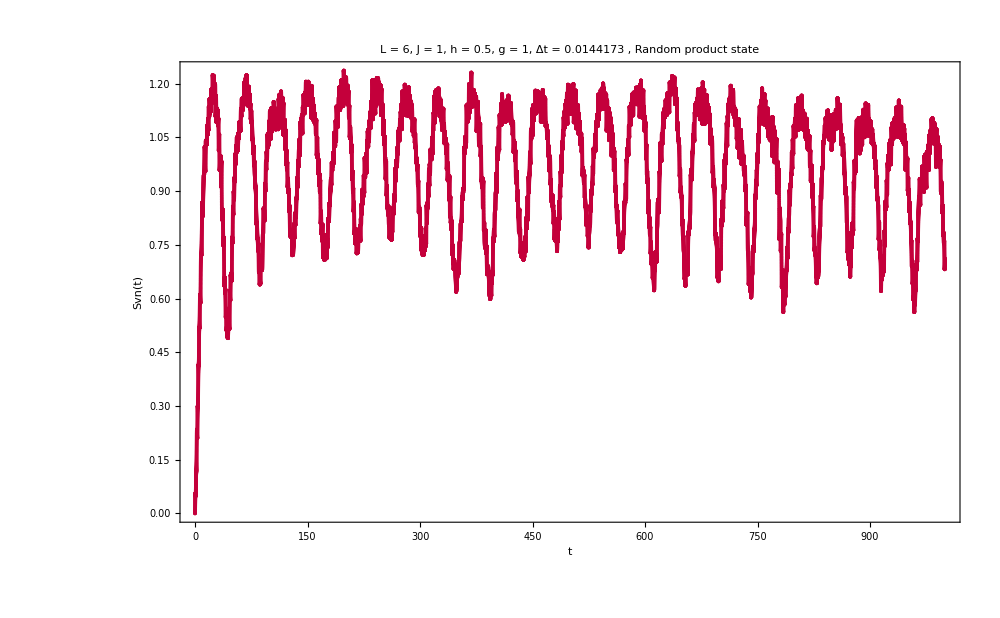

```mathematica
svnplots=ListPlot[entro1,PlotStyle->colors2[[-1]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

```mathematica
entropies=ParallelTable[svn[sortedrandoms[[All,2]][[1]],t],{t,tlist},DistributedContexts->Full];
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[All,2]]}];
```

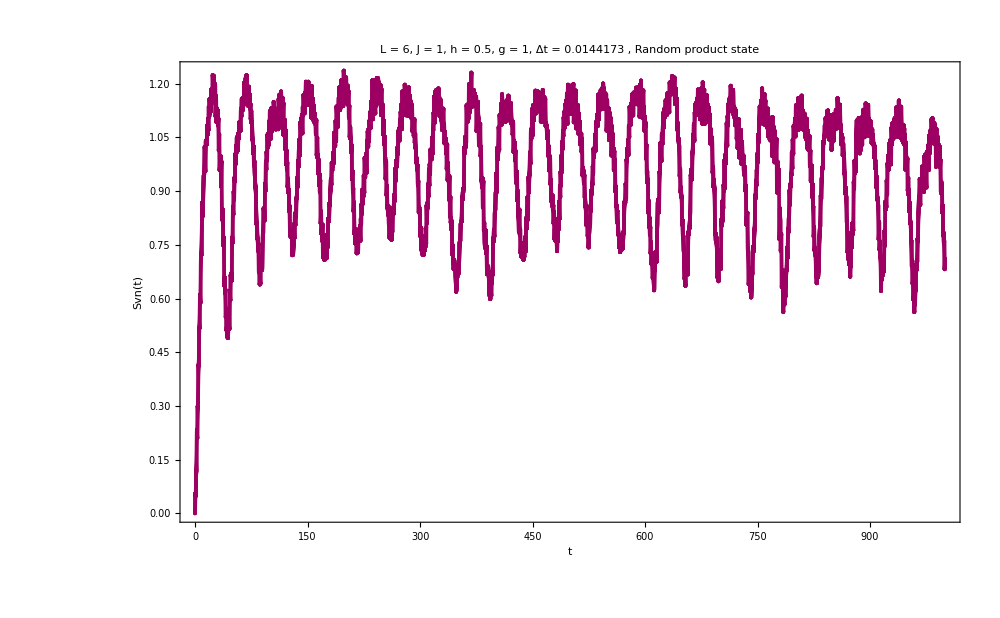

```mathematica
svnplots=ListPlot[entro1,PlotStyle->colors2[[1]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

# Random coherent states analysis

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=6;
g=J=1;
h=0.1;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
entropies=ParallelTable[svn[i,0],{i,eigenvec}];
```

```mathematica
data=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,1]]][[i]]}},{i,Length[eigenval]}];
data2=ParallelTable[{{scaledeigenval[[i]],Chop[entropies[[All,2]]][[i]]}},{i,Length[eigenval]}];
```

```mathematica
ListPlot[data,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
ListPlot[data2,PlotStyle->colors,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",|E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{l}",FontSize->35],Black]},ImageSize->800,PlotLegends->BarLegend[{custom,{Min[scaledeigenval],Max[scaledeigenval]}},LegendLabel->"Energy"]]
```

-Graphics-

-Graphics-

```mathematica
randoms=Table[coherentstate[RandomQubitState[],L],{i,2000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
rescaledNewValues=Rescale[energies,MinMax[eigenval],{0,1}];
```

```mathematica
entropydiag=ParallelTable[sdiag[i],{i,randoms}];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, coherent\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,rescaledNewValues}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, coherent\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[rescaledNewValues],Max[rescaledNewValues]}},LegendLabel->"Energy"]]
```

-Graphics-

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=1000;
tlist=Range[0,tf,Δt];
```

```mathematica
sortedrandoms=SortBy[Transpose[{Chop[entropydiag],randoms}],First];
```

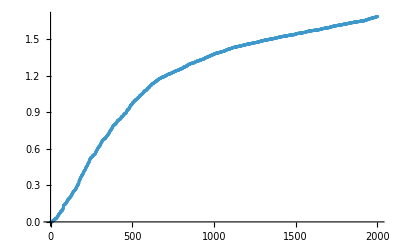

```mathematica
Sort[Chop[entropydiag]]//ListPlot
```

```mathematica
entropies=ParallelTable[svn[sortedrandoms[[All,2]][[-1]],t],{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Transpose[{tlist,entropies[[All,1]]}];
entro2=Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[All,2]]}];
```

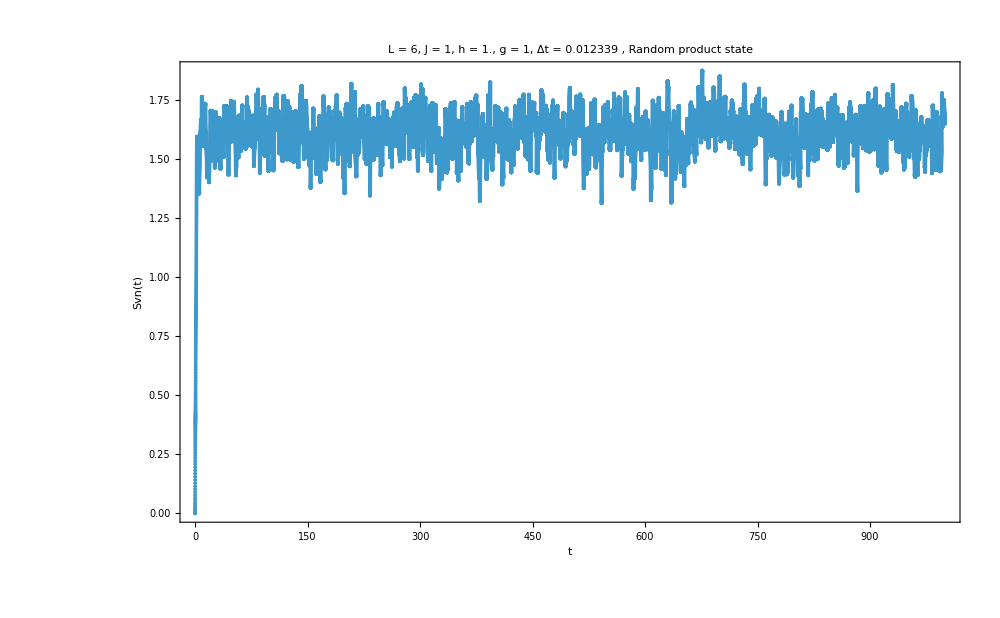

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

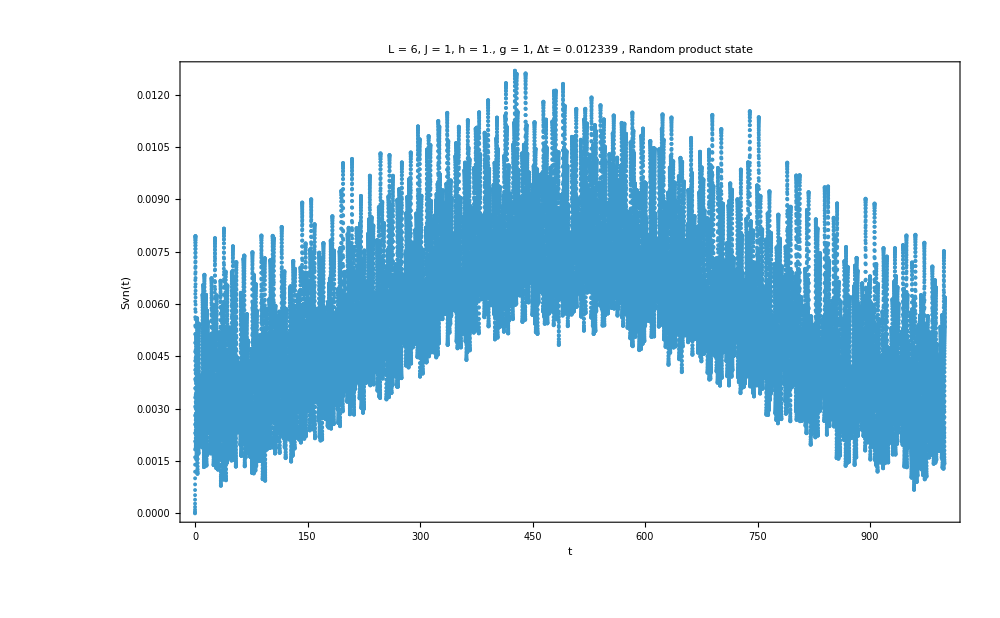

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

# Several random states

## Open

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Chop[Tr[rho.rho]];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-purity}
];
```

```mathematica
L=4;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
```

```mathematica
tlist=Range[0,(10),Δt];
tlist//Length
```

528

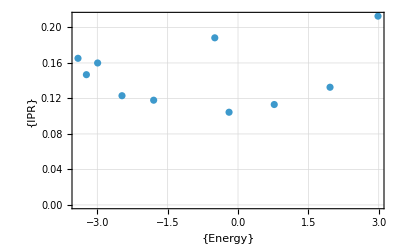

```mathematica
randoms=Table[RandomChainProductState[L],{i,10}];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=Table[Chop[Conjugate[i].H.i],{i,randoms}];
ListPlot[Transpose[{energies,iprs}],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{{"Energy"},{"IPR"}}]
```

```mathematica
entropies=ParallelTable[svn[j,t],{j,randoms},{t,tlist},DistributedContexts->Full];
```

```mathematica
entro1=Table[Transpose[{tlist,entropies[[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))entropies[[i]][[All,2]]}],{i,Length[randoms]}];
```

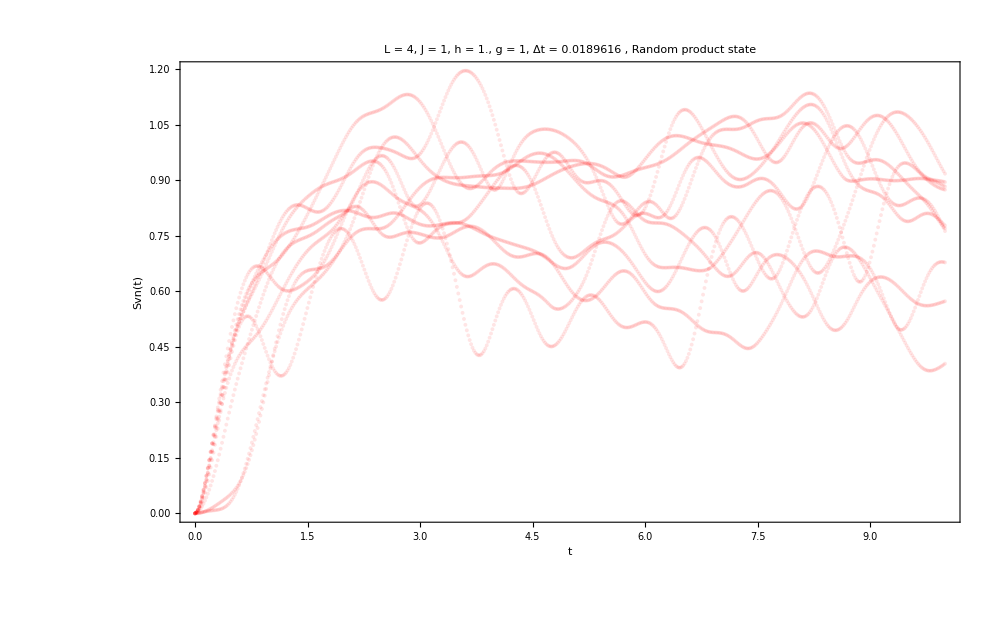

```mathematica
svnplots=ListPlot[entro1,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Red,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000]
```

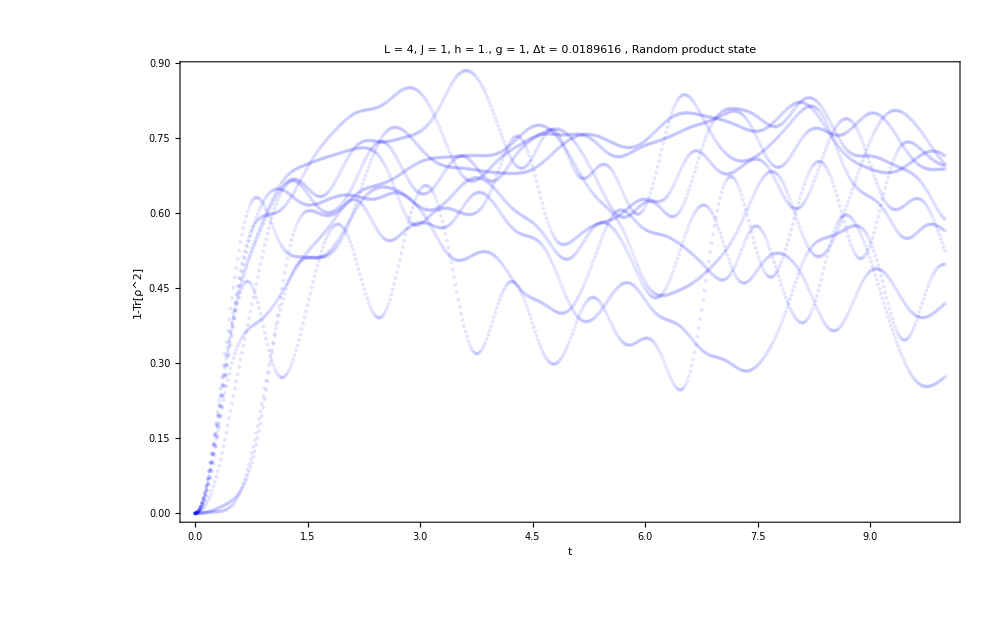

```mathematica
purityplots=ListPlot[entro2,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],PlotStyle->Directive[Blue,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["1-Tr[ρ^2]"]},PlotRange->All,ImageSize->1000]
```

# Results (Svn time series)

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity},
rho=MatrixPartialTrace[Dyad[state],1,{2^(L/2),2^(L/2)}];
purity=Tr[rho.rho];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[λ],1-Chop[purity]}
];
Clear[sdiag];
sdiag[ini_]:=Module[{state=Dyad[Conjugate[eigenvec].ini],rho,λ},
rho=MatrixPartialTrace[state,1,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
Clear[h,L];
(*I have data only for h=0.5,1*)
h=0.5;
J=g=1;
```

```mathematica
(*I have data for L = 4,6,8*)
L=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
(*H=IsingNNClosedHamiltonian[h,g,J,L];*)
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,(10^4),Δt];
```

```mathematica
texts={"closed","open"};
text=texts[[1]];
Clear[data1];
```

```mathematica
data1=Import["D:\\INVESTIGACION\\2025\\PCS\\Entropy\\entropies_withpurity_L_"<>ToString[L]<>"_"<>ToString[text]<>"chain_10_randomstates_h_"<>ToString[h]<>".m"];
```

```mathematica
randoms=data1[[1]];
```

```mathematica
entro1=Table[Transpose[{tlist,data1[[2]][[i]][[All,1]]}],{i,Length[randoms]}];
entro2=Table[Transpose[{tlist,(2^(L/2)/(2^(L/2)-1))data1[[2]][[i]][[All,2]]}],{i,Length[randoms]}];
```

```mathematica
meanssvn1=Table[Mean[i[[All,2]]],{i,entro1}];
meanspurity1=Table[Mean[i[[All,2]]],{i,entro2}];
diagonalentropies1=Table[sdiag[i],{i,randoms}];
```

```mathematica
(*This generates the plot of the comparison between the diagonal entropy and the time average for the 10 random initial states*)
```

```mathematica
fig1=ListPlot[{meanssvn1,diagonalentropies1},PlotTheme->"Detailed",Joined->True,PlotMarkers->Automatic,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" ,10 Random product state, "<>ToString[text]<>" chain",25,Black],PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},FrameLabel->{Style[MaTeX["i",FontSize->40],Black],Style[MaTeX["S",FontSize->40],Black]},FrameStyle->Directive[Black,FontSize->30],PlotRange->All,ImageSize->1000,PlotLegends->{Style[MaTeX["<S_{vn}>",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]}];
Export["entropycomparison_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>".png",fig1,ImageResolution->400]
```

entropycomparison_closedchain_L_8_h_0.5.png

```mathematica
(*This generates the plots of the Svn(t) for the 10 initial states*)
```

```mathematica
Do[
svnplots1=Show[{ListPlot[entro1[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, "<>ToString[text]<>" chain",20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->40],Black],Style[MaTeX["S_{vn}(t)",FontSize->40],Black]},PlotRange->All,ImageSize->1000],Plot[{meanssvn1[[q]],diagonalentropies1[[q]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},PlotLegends->{Style[MaTeX["<S_{vn}>",FontSize->30],Black],Style[MaTeX["S_{d}",FontSize->30],Black]}]},PlotRange->All];
Export["vnentropy_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>"_state_"<>ToString[q]<>".png",svnplots1,ImageResolution->400];
,{q,10}]
```

```mathematica
(*This generates the plots of the Sl(t) for the 10 initial states*)
```

```mathematica
Do[
svnplots1=Show[{ListPlot[entro2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state, "<>ToString[text]<>" chain",20,Black],PlotStyle->Directive[Gray,Opacity[0.1]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->40],Black],Style[MaTeX["1- Tr(\\hat{\\rho}_{B}^2)",FontSize->40],Black]},PlotRange->All,ImageSize->1000],Plot[meanspurity1[[q]],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Red]},PlotLegends->{Style[MaTeX["S_{l}",FontSize->30],Black]}]},PlotRange->All];
Export["purity_"<>ToString[text]<>"chain_L_"<>ToString[L]<>"_h_"<>ToString[h]<>"_state_"<>ToString[q]<>".png",svnplots1,ImageResolution->400];
,{q,10}]
```

# Averages comparison

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[meant];
 meant[T_]:=Mean[entro1[[1;;T]]][[2]];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];

Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
purity=Tr[rho.rho];
vn=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[vn],Chop[purity]}
];
Clear[Q];
Q[L_,La_,Lb_,eigenvec_,i_,j_]:=Q[L,La,Lb,eigenvec,i,j]=If[i<=j,Module[{projec=Dyad[eigenvec[[i]],eigenvec[[j]]],dima=2^(L-La),dimb=2^(L-Lb)},SparseArray[MatrixPartialTrace[projec,1,{dima,dimb}]]],ConjugateTranspose[Q[L,La,Lb,eigenvec,j,i]]];

Clear[meanpurity];
meanpurity[L_,La_,Lb_,ini_,eigenvec_]:=Module[{state=Conjugate[eigenvec].ini,dima=2^(L-La),dimb=2^(L-Lb),rho},
-Sum[(Abs[state[[i]]]^2)(Abs[state[[j]]]^2)Chop[Tr[Q[L,La,Lb,eigenvec,i,i].Q[L,La,Lb,eigenvec,j,j]]],{i,dima},{j,dima}]-Sum[(Abs[state[[i]]]^2)(Abs[state[[j]]]^2)Chop[Tr[Q[L,La,Lb,eigenvec,i,j].Q[L,La,Lb,eigenvec,j,i]]],{i,dima},{j,dima}]
];
```

```mathematica
L=8;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
randoms=Table[RandomChainProductState[L],{i,2000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,randoms},DistributedContexts->Full];
stdenergies=ParallelTable[Chop[Conjugate[i].(H.H).i],{i,randoms},DistributedContexts->Full];
varenergies=Table[Sqrt[stdenergies[[i]]-energies[[i]]^2],{i,Length[energies]}];
```

```mathematica
plist={4,3};
```

```mathematica
Do[
La=p;
Lb=L-La;
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
colors2=Table[Blend[{Blue,Red},i],{i,iprs}];
info=Table[{{energies[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[iprs],Max[iprs]}},LegendLabel->MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["scatter1_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300];
colors2=Table[Blend[{Blue,Red},i],{i,eigenval}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{E_i}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[eigenval],Max[eigenval]}},LegendLabel->MaTeX["E",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["scatter2_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300];
,{p,plist}];
```

```mathematica
meanpur=ParallelTable[1+meanpurity[L,La,Lb,i,eigenvec],{i,randoms}];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,iprs}];
info=Table[{{energies[[i]],meanpur[[i]]}},{i,Length[randoms]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["\\langle S_{2}\\rangle",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[iprs],Max[iprs]}},LegendLabel->MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35]]]
```

```mathematica
ListPlot[Transpose[{energies,varenergies}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["\\sigma_{E}",FontSize->35],Black]},ImageSize->800,PlotRange->All]
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,Rescale[Sort[entropydiag]]}];
sorted=Sort[entropydiag];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[entropydiag]]}];
ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Rescale[Sort[entropydiag]]],Max[Rescale[Sort[entropydiag]]]}},LegendLabel->MaTeX["S_{d}",FontSize->35]]]
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,Rescale[Sort[iprs]]}];
sorted=Sort[iprs];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[iprs]]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["IPR",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Rescale[Sort[iprs]]],Max[Rescale[Sort[iprs]]]}},LegendLabel->MaTeX[" ",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["iprs_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300]
```

iprs_openchain_L_8_La_4_h_1._states_5000.png

```mathematica
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
qlist={1,500,1000};
plist={1,2,3,4};
hlist=Range[0.05,1.05,0.05];
tf=1000;
```

```mathematica
randoms=Table[RandomChainProductState[L],{i,1000}];
```

```mathematica
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
colors2=Table[Blend[{Blue,Red},i],{i,Rescale[Sort[iprs]]}];
sorted=Sort[iprs];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[iprs]]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["IPR",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Rescale[Sort[iprs]]],Max[Rescale[Sort[iprs]]]}},LegendLabel->MaTeX[" ",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["iprs_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300];

Do[

La=p;
Lb=L-La;

Do[

difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tlist=Range[0,tf,Δt];
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
sortedrandoms=SortBy[Transpose[{Chop[iprs],randoms,entropydiag}],First];
ini=sortedrandoms[[q,2]];

entropies=ParallelTable[svn[L,La,Lb,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
entro1=Transpose[{tlist,entropies}];
(*entro2=Transpose[{tlist,1-entropies[[All,2]]}];
sortedpurities=SortBy[Transpose[{Chop[entropydiag],meanpur}],First];
fInterp = Interpolation[entro2]; 
 mean=NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]];
slplots=Show[{ListPlot[entro2,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["S_{l}",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedpurities[[q,1]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]}]},PlotRange->All]*)
data=ParallelTable[{tlist[[i]],meant[i]},{i,2,Length[tlist],1000},DistributedContexts->Full];
fInterp = Interpolation[entro1]; 
 mean=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];

figure1=Show[{ListPlot[entro1,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, state \\,"<>ToString[q],FontSize->35],Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["S_{vn}(t)",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedrandoms[[q,3]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]},PlotLegends->{Style[MaTeX["S_d = "<>ToString[sortedrandoms[[q,3]]],FontSize->35],Black],Style[MaTeX["\\langle S_{vn} \\rangle = "<>ToString[mean],FontSize->35],Black]}]},PlotRange->All];
figure2=Show[{ListPlot[data,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, state \\,"<>ToString[q],FontSize->35],Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["\\langle S_{vn}\\rangle(t)",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedrandoms[[q,3]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]},PlotLegends->{Style[MaTeX["S_d = "<>ToString[sortedrandoms[[q,3]]],FontSize->35],Black],Style[MaTeX["\\langle S_{vn} \\rangle = "<>ToString[mean],FontSize->35],Black]}]},PlotRange->All];
Export["svnt_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[q]<>".png",figure1,ImageResolution->300];
Export["meansvnt_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[q]<>".png",figure2,ImageResolution->300];

,{q,qlist}];
,{p,plist}];
,{h,hlist}];
```

$Aborted

# IPR as the difference between Sd and <Svn>

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[meant];
 meant[T_,list_]:=Mean[list[[1;;T]]][[2]];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];

(*Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
purity=Tr[rho.rho];
vn=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[vn],Chop[purity]}
];*)
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[Q];
Q[L_,La_,Lb_,eigenvec_,i_,j_]:=Q[L,La,Lb,eigenvec,i,j]=If[i<=j,Module[{projec=Dyad[eigenvec[[i]],eigenvec[[j]]],dima=2^(L-La),dimb=2^(L-Lb)},SparseArray[MatrixPartialTrace[projec,1,{dima,dimb}]]],ConjugateTranspose[Q[L,La,Lb,eigenvec,j,i]]];

Clear[meanpurity];
meanpurity[L_,La_,Lb_,ini_,eigenvec_]:=Module[{state=Conjugate[eigenvec].ini,dima=2^(L-La),dimb=2^(L-Lb),rho},
-Sum[(Abs[state[[i]]]^2)(Abs[state[[j]]]^2)Chop[Tr[Q[L,La,Lb,eigenvec,i,i].Q[L,La,Lb,eigenvec,j,j]]],{i,dima},{j,dima}]-Sum[(Abs[state[[i]]]^2)(Abs[state[[j]]]^2)Chop[Tr[Q[L,La,Lb,eigenvec,i,j].Q[L,La,Lb,eigenvec,j,i]]],{i,dima},{j,dima}]
];
```

```mathematica
L=6;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
scaledeigenval=Rescale[eigenval+Abs[eigenval[[1]]]];
colors=Table[Blend[{Blue,Red},i],{i,scaledeigenval}];
custom[x_]:=Blend[{Blue,Red},x];
```

```mathematica
randoms=Table[RandomChainProductState[L],{i,2000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,randoms}];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,randoms},DistributedContexts->Full];
(*stdenergies=ParallelTable[Chop[Conjugate[i].(H.H).i],{i,randoms},DistributedContexts->Full];
varenergies=Table[Sqrt[stdenergies[[i]]-energies[[i]]^2],{i,Length[energies]}];*)
```

```mathematica
La=3;
Lb=L-La;
entropydiag=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,randoms},DistributedContexts->Full];
colors2=Table[Blend[{Blue,Red},i],{i,iprs}];
info=Table[{{energies[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[iprs],Max[iprs]}},LegendLabel->MaTeX["IPR_{|E_{i}\\rangle}",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["scatter1_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300];
colors2=Table[Blend[{Blue,Red},i],{i,eigenval}];
info=Table[{{iprs[[i]],entropydiag[[i]]}},{i,Length[randoms]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["IPR_{E_i}",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[eigenval],Max[eigenval]}},LegendLabel->MaTeX["E",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["scatter2_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300];
```

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,Rescale[Sort[entropydiag]]}];
sorted=Sort[entropydiag];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[entropydiag]]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["S_{d}",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Rescale[Sort[entropydiag]]],Max[Rescale[Sort[entropydiag]]]}},LegendLabel->MaTeX["S_{d}",FontSize->35]]];
Export["entropydiag_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300]
```

entropydiag_openchain_L_6_La_3_h_1._states_2000.png

```mathematica
colors2=Table[Blend[{Blue,Red},i],{i,Rescale[Sort[iprs]]}];
sorted=Sort[iprs];
info=Table[{{i,sorted[[i]]}},{i,Length[Sort[iprs]]}];
figure=ListPlot[info,PlotStyle->colors2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, states",FontSize->35],Black],FrameLabel->{Style[MaTeX["i",FontSize->35],Black],Style[MaTeX["IPR",FontSize->35],Black]},ImageSize->800,PlotRange->All,PlotLegends->BarLegend[{custom,{Min[Rescale[Sort[iprs]]],Max[Rescale[Sort[iprs]]]}},LegendLabel->MaTeX[" ",FontSize->35]],FrameStyle->Directive[Black,20]];
Export["iprs_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[Length[randoms]]<>".png",figure,ImageResolution->300]
```

iprs_openchain_L_6_La_3_h_1._states_2000.png

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=1000;
tlist=Range[0,tf,Δt];
sortedrandoms=SortBy[Transpose[{entropydiag,randoms,iprs}],First];
```

```mathematica
q=2000;
ini=sortedrandoms[[q,2]];
entropies=ParallelTable[svn[L,La,Lb,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
entro1=Transpose[{tlist,entropies}];
fInterp = Interpolation[entro1]; 
 mean=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]];
data=ParallelTable[{tlist[[i]],meant[i,entro1]},{i,2,Length[tlist],1000},DistributedContexts->Full];
```

```mathematica
figure1=Show[{ListPlot[entro1,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, state \\,"<>ToString[q],FontSize->35],Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["S_{vn}(t)",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedrandoms[[q,1]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]},PlotLegends->{Style[MaTeX["S_d = "<>ToString[sortedrandoms[[q,1]]],FontSize->35],Black],Style[MaTeX["\\langle S_{vn} \\rangle = "<>ToString[mean],FontSize->35],Black]}]},PlotRange->All];
figure2=Show[{ListPlot[data,PlotStyle->colors2[[q]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>",\\, L_{a} = "<>ToString[La]<>" \\, ,Random\\, product\\, state \\,"<>ToString[q],FontSize->35],Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style[MaTeX["t",FontSize->35],Black],Style[MaTeX["\\langle S_{vn}\\rangle(t)",FontSize->35],Black]},PlotRange->All,ImageSize->1000],Plot[{sortedrandoms[[q,1]],mean},{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Gray,Dashed],Directive[Brown,Dashed]},PlotLegends->{Style[MaTeX["S_d = "<>ToString[sortedrandoms[[q,1]]],FontSize->35],Black],Style[MaTeX["\\langle S_{vn} \\rangle = "<>ToString[mean],FontSize->35],Black]}]},PlotRange->All];
Export["svnt_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[q]<>".png",figure1,ImageResolution->300];
Export["meansvnt_openchain_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_h_"<>ToString[h]<>"_states_"<>ToString[q]<>".png",figure2,ImageResolution->300];
```

# Single product state

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
(*purity=Tr[rho.rho];
vn=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]];
{Chop[vn],Chop[purity]}*)
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
L=8;
g=J=1;
h=1.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
La=4;
Lb=L-La;
diagentro=ParallelTable[Chop[sdiag[L,La,Lb,i]],{i,eigenvec}];
```

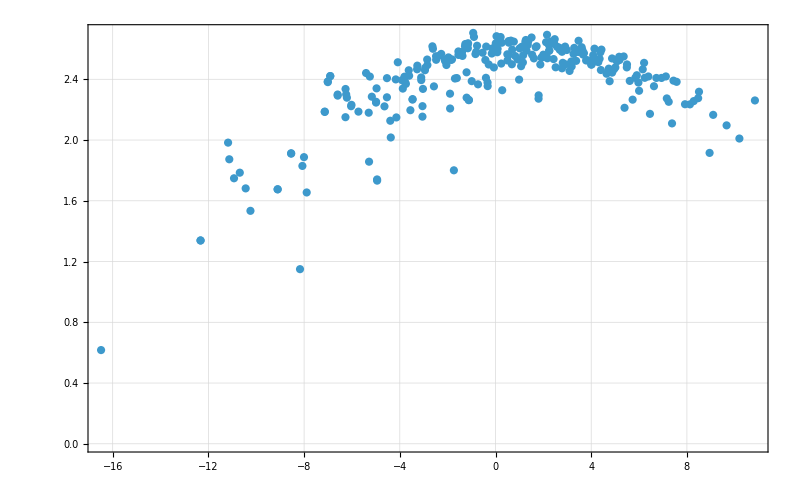

```mathematica
ListPlot[Transpose[{eigenval,diagentro}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>", La = "<>ToString[La]<>", |E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,FrameStyle->Directive[Black,20]]
```

```mathematica
difs=Outer[Subtract,eigenval,eigenval];
maxdif=Max[Abs[difs]];
Δt=1/(4*maxdif);
tf=500;
tlist=Range[0,tf,Δt];
tlist//Length
```

33184

```mathematica
tlist=Range[100000,100500,Δt];
tlist//Length
```

33184

```mathematica
tlist=Table[10^i,{i,0,10,0.01}];
```

```mathematica
inistate=RandomChainProductState[L];
```

```mathematica
svnt=Table[ParallelTable[{t,svn[L,i,L-i,inistate,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,1,L-1}];
```

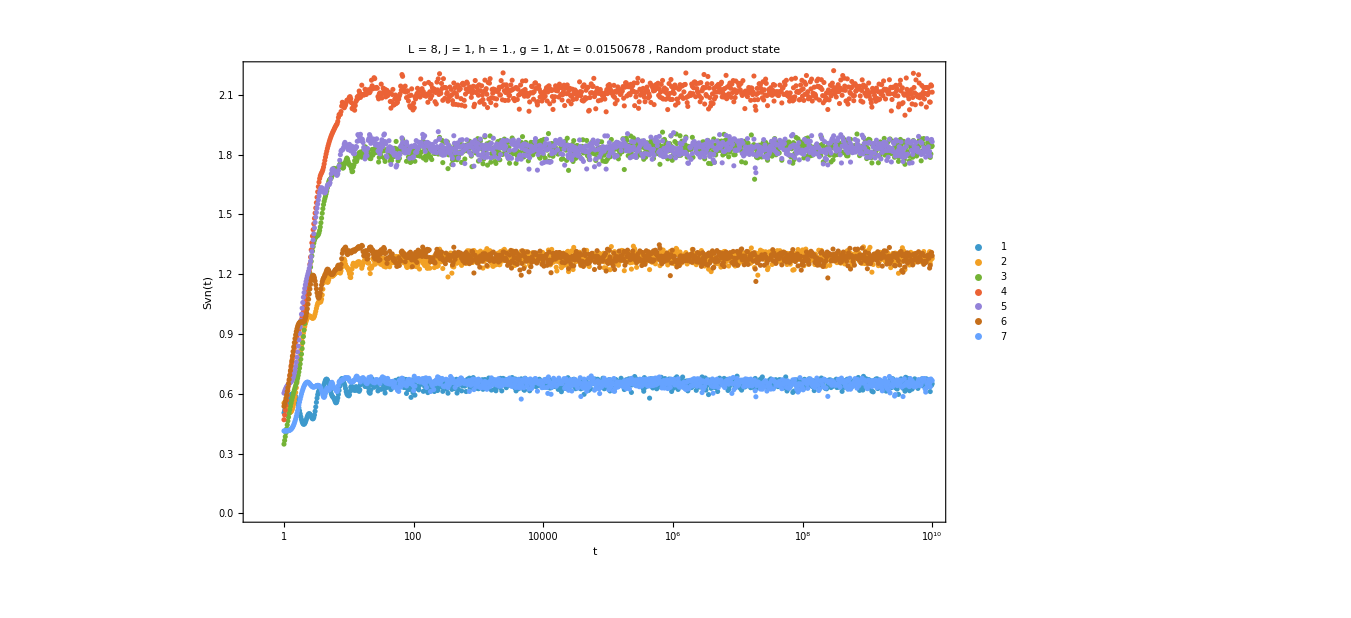

```mathematica
svnplots=ListLogLinearPlot[svnt,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic]
```

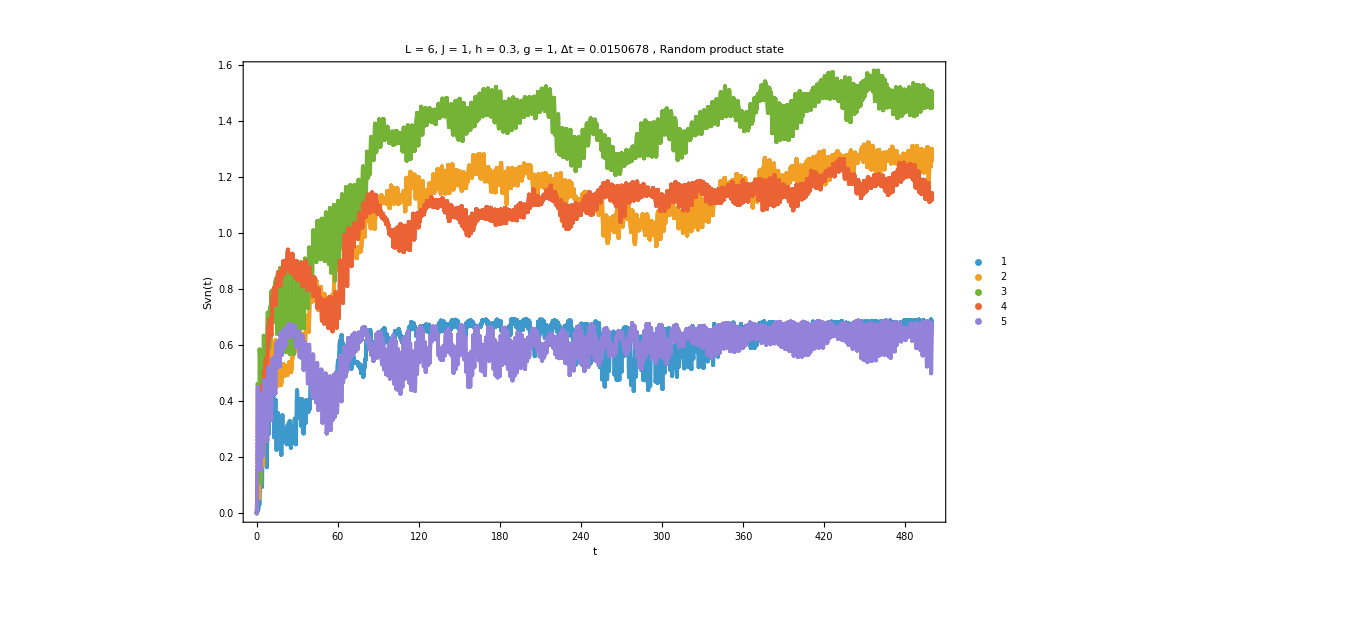

```mathematica
svnplots=ListPlot[svnt,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Δt = "<>ToString[Δt]<>" , Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic]
```

```mathematica
Clear[meant,fInterp,mean];
 meant[T_]:=Mean[entro1[[1;;T]]][[2]];
```

```mathematica
fInterp = Interpolation[entro1]; 
 mean=Quiet[NIntegrate[fInterp[t],{t,tlist[[1]],tlist[[-1]]}]/tlist[[-1]]]
```

```mathematica
energy=Chop[ConjugateTranspose[inistate].H.inistate]
```

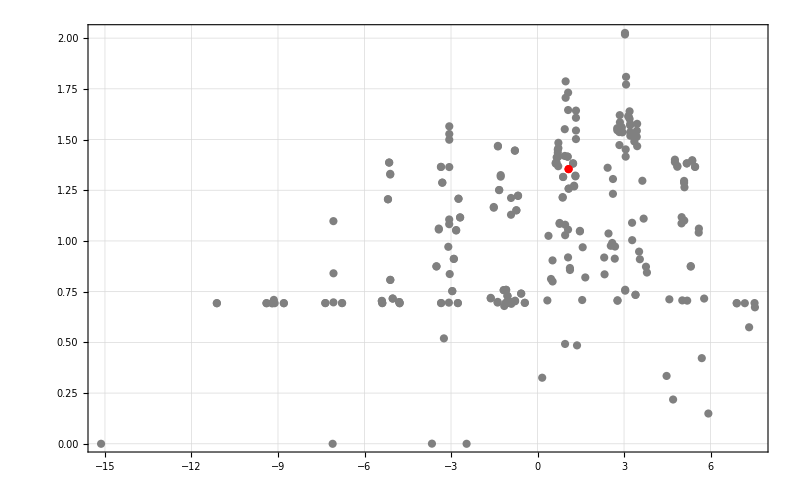

```mathematica
ListPlot[{Transpose[{eigenval,diagentro}],{Transpose[{energy,mean}]}},PlotStyle->{Directive[Gray],Directive[Red]},PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>", La = "<>ToString[La]<>", |E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,FrameStyle->Directive[Black,20],PlotRange->All]
```

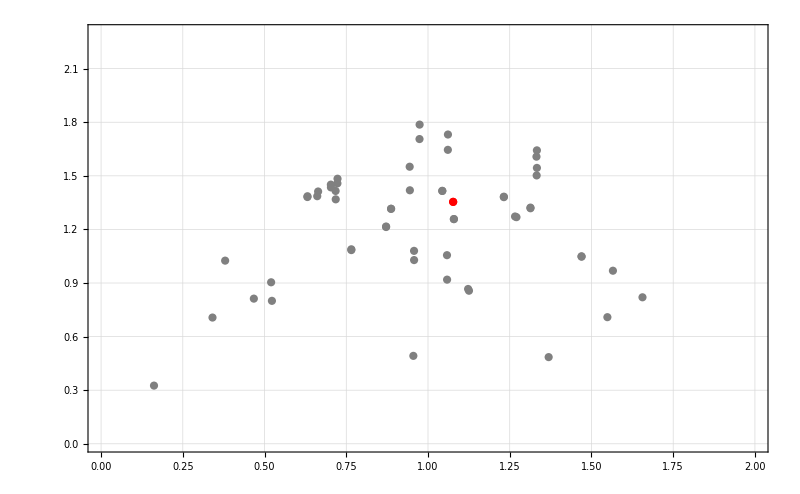

```mathematica
ListPlot[{Transpose[{eigenval,diagentro}],{Transpose[{energy,mean}]}},PlotStyle->{Directive[Gray],Directive[Red]},PlotTheme->"Detailed",PlotLabel->Style[MaTeX["h = "<>ToString[h]<>" \\,, L="<>ToString[L]<>", La = "<>ToString[La]<>", |E_{i}\\rangle",FontSize->35],Black],FrameLabel->{Style[MaTeX["E",FontSize->35],Black],Style[MaTeX["S_{vn}",FontSize->35],Black]},ImageSize->800,FrameStyle->Directive[Black,20],PlotRange->{{0,2},{0,2.3}}]
```

```mathematica
selected=Select[Transpose[{eigenval,diagentro}],0<=#[[1]]<=2&];
selected//Length
```

55

```mathematica
meaneigenvec=Mean[selected[[All,2]]]
stdeigenvec=StandardDeviation[selected[[All,2]]]
```

1.21441

0.329488

```mathematica
mean
```

1.3542

```mathematica
inistateeigen=Conjugate[eigenvec].inistate;
```

```mathematica
sdiag[L,La,Lb,inistateeigen]
```

2.1733

```mathematica
Clear[Q];
Q[L_,La_,Lb_,eigenvec_,i_,j_]:=Module[{projec=Dyad[eigenvec[[i]],eigenvec[[j]]],dima=2^(L-La),dimb=2^(L-Lb)},
SparseArray[MatrixPartialTrace[projec,1,{dima,dimb}]]];
```

```mathematica
newrhodiag=Sum[(Abs[inistateeigen[[i]]]^2)Q[L,La,Lb,eigenvec,i,i],{i,2^L}];
```

```mathematica
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[newrhodiag]]]]]]
```

2.59773

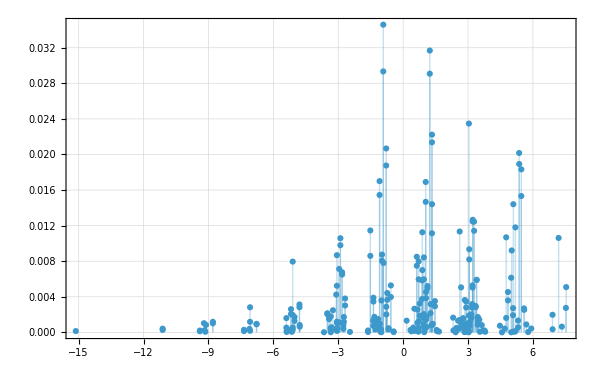

```mathematica
ListPlot[Transpose[{eigenval,Abs[inistateeigen]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600]
```

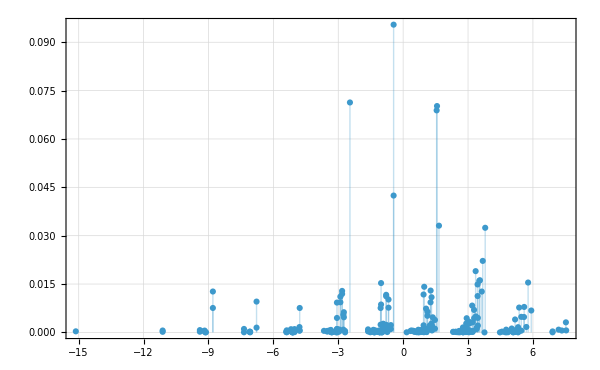

```mathematica
ListPlot[Transpose[{eigenval,Abs[Conjugate[eigenvec].RandomChainProductState[L]]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600]
```

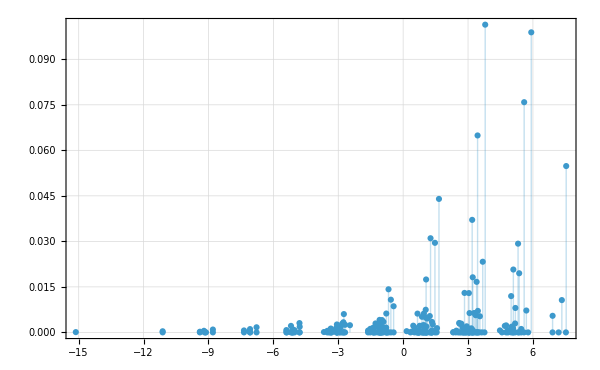

```mathematica
ListPlot[Transpose[{eigenval,Abs[Conjugate[eigenvec].coherentstate[RandomChainProductState[1],L]]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600]
```